```mathematica
x[t]=(l/2)*Cos[θ[t]]
```

1/2 l Cos[θ[t]]

```mathematica
D[D[x[t],t],t]//FullSimplify
```

-1/2 l (Cos[θ[t]] θ'[t]^2+Sin[θ[t]] θ''[t])

```mathematica
y[t]=(l/2)*Sin[θ[t]]
```

1/2 l Sin[θ[t]]

```mathematica
D[D[y[t],t],t]//FullSimplify
```

1/2 (-l Sin[θ[t]] θ'[t]^2+l Cos[θ[t]] θ''[t])

```mathematica
Solve[m*D[D[x[t],t],t]==λ1,λ1][[1]]
```

{λ1→-1/2 m (l Cos[θ[t]] θ'[t]^2+l Sin[θ[t]] θ''[t])}

```mathematica
Solve[m*D[D[y[t],t],t]+m*g==λ2,λ2][[1]]
```

{λ2→1/2 (2 g m-l m Sin[θ[t]] θ'[t]^2+l m Cos[θ[t]] θ''[t])}

```mathematica
λ1=-1/2 m (l Cos[θ[t]] θ'[t]^2+l Sin[θ[t]] θ''[t])
```

-1/2 m (l Cos[θ[t]] θ'[t]^2+l Sin[θ[t]] θ''[t])

```mathematica
λ2=1/2 (2 g m-l m Sin[θ[t]] θ'[t]^2+l m Cos[θ[t]] θ''[t])
```

1/2 (2 g m-l m Sin[θ[t]] θ'[t]^2+l m Cos[θ[t]] θ''[t])

```mathematica
Solve[FullSimplify[θ''[t]*m*l^2/12==λ1*(l/2)*Sin[θ[t]]-λ2*(l/2)*Cos[θ[t]]],θ''[t]]
```

{{θ''[t]→-(3 g Cos[θ[t]])/(2 l)}}

```mathematica
Solve[θ''[t]*m*l^2/12==-1/2 (2 g m-l m Sin[θ[t]] θ'[t]^2+l m Cos[θ[t]] θ''[t])*Cos[θ[t]]*l/2,θ''[t]]//FullSimplify
```

{{θ''[t]→(3 Cos[θ[t]] (-2 g+l Sin[θ[t]] θ'[t]^2))/(l+3 l Cos[θ[t]]^2)}}

```mathematica
Solve[θ''[t]*m*l^2/12==-1/2 (2 g m-l m Sin[θ[t]] θ'[t]^2+l m Cos[θ[t]] θ''[t])*Cos[θ[t]]*l/2,θ''[t]]//FullSimplify
```

{{θ''[t]→(3 Cos[θ[t]] (-2 g+l Sin[θ[t]] θ'[t]^2))/(l+3 l Cos[θ[t]]^2)}}

```mathematica
tEnd=Re[Integrate[-1/Sqrt[-3*9.8/3*(Sin[Theta]-Sin[Pi/3])],{Theta,Pi/3,ArcSin[(2/3)*Sin[Pi/3]]}]]
```

0.563257

```mathematica
l=3;
g=9.8;
```

```mathematica
s=NDSolve[{θ''[t]==(-3*g/(2*l))*Cos[θ[t]],θ[0]==Pi/3,θ'[0]==0},
θ[t],{t,0,tEnd}]
```

{{θ[t]→InterpolatingFunction[…][t]}}

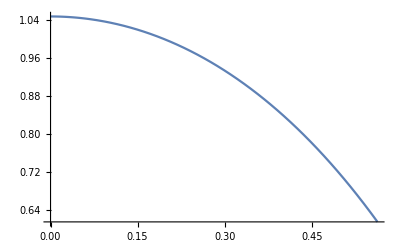

```mathematica
Plot[Evaluate[θ[t]/. s],{t,0,tEnd},PlotRange->All]
```

```mathematica
s2=NDSolve[{θ1''[t]==3*Cos[θ1[t]]*(-2*g/l + Sin[θ1[t]]*θ1'[t]^2)/(3*Cos[θ1[t]]^2+1),
θ1[tEnd]==ArcSin[(2/3)*Sin[Pi/3]],
θ1'[tEnd]==-Sqrt[(3*g/l)*(Sin[Pi/3]-Sin[ArcSin[(2/3)*Sin[Pi/3]]])]},
θ1[t],{t,tEnd,1}]
```

{{θ1[t]→InterpolatingFunction[…][t]}}

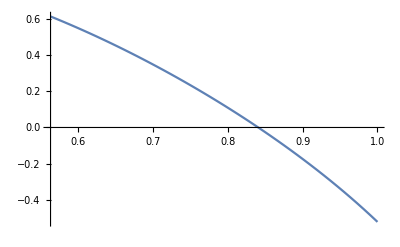

```mathematica
Plot[Evaluate[θ1[t]/. s2],{t,tEnd,1},PlotRange->All]
```

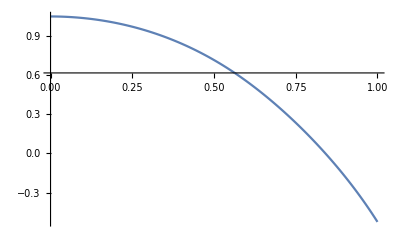

```mathematica
Show[Plot[Evaluate[θ[t]/. s],{t,0,tEnd},PlotRange->All],
Plot[Evaluate[θ1[t]/. s2],{t,tEnd,1},PlotRange->All]]
```

```mathematica
(*Part g*)
```

```mathematica
λ2=(1/2)(2 g m-l m Sin[θ[t]] θ'[t]^2+l m Cos[θ[t]] θ''[t])/.{θ''[t]->(3 Cos[θ[t]] (-2 g+l Sin[θ[t]] θ'[t]^2))/(l+3 l Cos[θ[t]]^2)}//FullSimplify
```

(m (2 g-l Sin[θ[t]] θ'[t]^2))/(2+6 Cos[θ[t]]^2)

```mathematica
ThetaPrime=Solve[(1/2)*m*(l/2)^2*Cos[θ[t]]^2*θ'[t]^2-m*g*(l/2)*Sin[θ[t]]+(1/2)*(1/12)*m*l^2*θ'[t]^2
==
(1/2)*m*((l/2)*(Cos[ArcSin[(2/3)*Sin[θ0]]])*Sqrt[((3*g/l)*(Sin[θ0]-(2/3)*Sin[θ0]))])^2-m*g*(l/2)*(2/3)*Sin[θ0]+(1/2)*(1/12)*m*l^2*(3*g/l)*(Sin[θ0]-(2/3)*Sin[θ0]),θ'[t]][[2]]
```

{θ'[t]→(2 √(-3 g Sin[θ0]-g Sin[θ0]^3+9 g Sin[θ[t]]))/(√3 √(l+3 l Cos[θ[t]]^2))}

```mathematica
ThetaPrime=ThetaPrime[[1]]
```

θ'[t]→(2 √(-3 g Sin[θ0]-g Sin[θ0]^3+9 g Sin[θ[t]]))/(√3 √(l+3 l Cos[θ[t]]^2))

```mathematica
(m (2 g-l Sin[θ[t]] θ'[t]^2))/(2+6 Cos[θ[t]]^2)/.{ThetaPrime}//FullSimplify
```

(g m (3+9 Cos[θ[t]]^2+2 (3 Sin[θ0]+Sin[θ0]^3-9 Sin[θ[t]]) Sin[θ[t]]))/(3 (1+3 Cos[θ[t]]^2)^2)

```mathematica
(g m (3+9 Cos[θ[t]]^2+2 (3 Sin[θ0]+Sin[θ0]^3-9 Sin[θ[t]]) Sin[θ[t]]))/(3 (1+3 Cos[θ[t]]^2)^2)//FullSimplify//TeXForm
```

\frac{g m \left(2 \sin (\theta (t)) \left(\sin ^3(\text{$\theta $0})+3 \sin
   (\text{$\theta $0})-9 \sin (\theta (t))\right)+9 \cos ^2(\theta (t))+3\right)}{3
   \left(3 \cos ^2(\theta (t))+1\right)^2}

```mathematica
hEnd=Pi/1000;
```

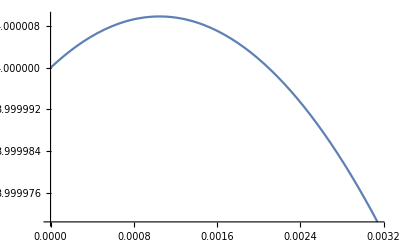

```mathematica
Plot[4+2*Sin[h](3*Sin[hEnd]+Sin[hEnd]^3-(9/2)*Sin[h]),{h,0,hEnd}]
```

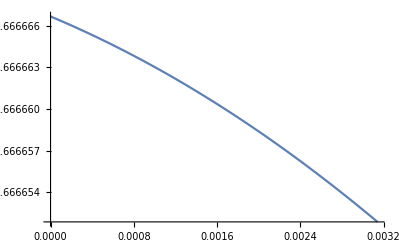

```mathematica
Plot[5/3-(1/2)*Sin[h]^2-Sin[h]*Sin[hEnd],{h,0,hEnd}]
```